```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["ErrorBarPlots`"];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Generate Spectral Functions

```mathematica
R=20000;
Mc=1.4690612135716832;
Mb=4.882;
kfinal={0.4709613222916442,-0.2550225519531524};
kfinalu={0.8020780608066254,-0.360468820434673};
kfinall={0.13984458377666326,-0.14957628347163182};
αcont={0.5137193759431391,0.0024666827878353577}; 
σcont={0.16955497884544793,0.0008581023195660334};
ccont={-0.15956635071361625,0.0024752900407607015};
```

### Define required functions

```mathematica
g[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
ϕ[x_]:=Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[x z],{z,0,∞}]];
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c
ReVm0[r_,α_,σ_,c_]:=-α/r+σ r+c
```

```mathematica
Clear[ParabolicCylinderI,ParabolicCylinderR];
ParabolicCylinderI[r_]=If[r<20,ParabolicCylinderD[-1/2,ⅈ √2 r],ⅇ^(r^2/2) (((1-ⅈ) √(1/r))/2^(3/4)+((3/16-(3 ⅈ)/16) (1/r)^(5/2))/2^(3/4)+((105/512-(105 ⅈ)/512) (1/r)^(9/2))/2^(3/4)+((3465/8192-(3465 ⅈ)/8192) (1/r)^(13/2))/2^(3/4)+((675675/524288-(675675 ⅈ)/524288) (1/r)^(17/2))/2^(3/4))];
ParabolicCylinderR[r_]=ParabolicCylinderD[-1/2,√2 r];
```

```mathematica
ϵ=1/1000;ϕ1table=Quiet[ Join[Parallelize[Table[{x,1-ϕ[x]},{x,ϵ/100,2,10ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,2+100ϵ,10,100ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,10+1000ϵ,100,10000ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,100+100000ϵ,10000,100000ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,10000+10000000ϵ,1000000,10000000ϵ}]]]];
```

```mathematica
TableT[σ1_,α1_, mD1_]:=Module[{σ=σ1, α=α1,mD=mD1,r,μ,c1},
μ=(mD^2 σ/α)^(1/4);
r=mD/μ;
pg=1;
c1=Re[ParabolicCylinderI[ϵ/100]NIntegrate[ParabolicCylinderR[x] x^2 g[x r],{x,0,∞},PrecisionGoal->pg]];
ψ1[x_,r_]:=c1-ParabolicCylinderR[x]NIntegrate[y^2 g[y r]Re[ParabolicCylinderI[y]],{y,0,x},PrecisionGoal->pg]-Re[ParabolicCylinderI[x]]NIntegrate[ParabolicCylinderR[y] y^2 g[y r],{y,x,∞},PrecisionGoal->pg];
ψ1table=Join[Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,ϵ/100,1,10ϵ}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,1+100ϵ,10+ϵ,100ϵ}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,11,100,1}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,200,1000,100}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,2000,20000,1000}]]];];
```

```mathematica
mDcalmu[T_,μ_,c_,d_]:=Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ];
```

### Modules

```mathematica
swaveccspectra[n_,Tmuscan_]:=Module[{s=Tmuscan[[n,1]],T=Tmuscan[[n,2]],μ=Tmuscan[[n,3]],mD=mDcalmu[Tmuscan[[n,2]],Tmuscan[[n,3]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ρtable,ccsT,Tstring,μstring},
TableT[σ,α,mD];

rev=Interpolation[Join[Table[{r,ReV[r,mD,α,σ,c]},{r,0.001,10,0.01}],Table[{r,ReV[r,mD,α,σ,c]},{r,10.1,25,0.1}],Table[{r,ReV[r,mD,α,σ,c]},{r,26,1000,1}],Table[{r,ReV[r,mD,α,σ,c]},{r,1010,20000,10}]]];
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
ψ1inter=Interpolation[ψ1table,InterpolationOrder->1];
V[x_]:=rev[x]+ⅈ (α T ϕ1[mD x]+α T ψ1inter[(mD^2 σ/α)^(1/4) x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=2;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];

ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

ccsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];
Export["spectraldata/Snnscan/cc/swccs"<>ToString[s]<>"spectra.dat",ccsT]
]
```

```mathematica
swaveccuspectra[n_,Tmuscan_]:=Module[{s=Tmuscan[[n,1]],T=Tmuscan[[n,2]],μ=Tmuscan[[n,3]],mD=mDcalmu[Tmuscan[[n,2]],Tmuscan[[n,3]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ρtable,ccsT,Tstring,μstring},
TableT[σ,α,mD];

rev=Interpolation[Join[Table[{r,ReV[r,mD,α,σ,c]},{r,0.001,10,0.01}],Table[{r,ReV[r,mD,α,σ,c]},{r,10.1,25,0.1}],Table[{r,ReV[r,mD,α,σ,c]},{r,26,1000,1}],Table[{r,ReV[r,mD,α,σ,c]},{r,1010,20000,10}]]];
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
ψ1inter=Interpolation[ψ1table,InterpolationOrder->1];
V[x_]:=rev[x]+ⅈ (α T ϕ1[mD x]+α T ψ1inter[(mD^2 σ/α)^(1/4) x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=2;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];

ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

ccsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];
Export["spectraldata/Snnscan/cc/swccs"<>ToString[s]<>"uspectra.dat",ccsT]
]
```

```mathematica
swavecclspectra[n_,Tmuscan_]:=Module[{s=Tmuscan[[n,1]],T=Tmuscan[[n,2]],μ=Tmuscan[[n,3]],mD=mDcalmu[Tmuscan[[n,2]],Tmuscan[[n,3]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ρtable,ccsT,Tstring,μstring},
TableT[σ,α,mD];

rev=Interpolation[Join[Table[{r,ReV[r,mD,α,σ,c]},{r,0.001,10,0.01}],Table[{r,ReV[r,mD,α,σ,c]},{r,10.1,25,0.1}],Table[{r,ReV[r,mD,α,σ,c]},{r,26,1000,1}],Table[{r,ReV[r,mD,α,σ,c]},{r,1010,20000,10}]]];
ϕ1=Interpolation[ϕ1table,InterpolationOrder->1];
ψ1inter=Interpolation[ψ1table,InterpolationOrder->1];
V[x_]:=rev[x]+ⅈ (α T ϕ1[mD x]+α T ψ1inter[(mD^2 σ/α)^(1/4) x]);

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=2;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable];

ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

ccsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];
Export["spectraldata/Snnscan/cc/swccs"<>ToString[s]<>"lspectra.dat",ccsT]
]
```

### Statistical model √s_NN

```mathematica
(* s here is √Subscript[s, NN] in GeV*)
T[s_]:=Tlim 1/(1+Exp[1.72-Log[s/0.45]]);
μ[s_]:=(1303 10^-3)/(1+0.286 s);
Tlim=0.155;
```

```mathematica
Tmuscan=Join[Table[{i,T[i],μ[i]},{i,8,195,10}],Table[{i,T[i],μ[i]},{i,200,1000,100}],Table[{i,T[i],μ[i]},{i,2000,10000,1000}]]
```

{{8,0.117949,0.39629},{18,0.136011,0.211939},{28,0.142234,0.144649},{38,0.145385,0.109791},{48,0.147289,0.0884709},{58,0.148563,0.0740846},{68,0.149476,0.0637226},{78,0.150162,0.0559036},{88,0.150697,0.0497936},{98,0.151125,0.0448877},{108,0.151475,0.0408618},{118,0.151768,0.0374986},{128,0.152015,0.0346469},{138,0.152228,0.0321983},{148,0.152412,0.0300729},{158,0.152573,0.0282108},{168,0.152716,0.0265658},{178,0.152842,0.0251021},{188,0.152955,0.0237913},{200,0.153077,0.0223883},{300,0.153712,0.0150115},{400,0.154032,0.0112912},{500,0.154225,0.00904861},{600,0.154354,0.00754925},{700,0.154446,0.00647614},{800,0.154515,0.00567015},{900,0.154568,0.00504257},{1000,0.154611,0.00454007},{2000,0.154805,0.002274},{3000,0.15487,0.00151688},{4000,0.154903,0.00113799},{5000,0.154922,0.000910552},{6000,0.154935,0.000758882},{7000,0.154944,0.000650524},{8000,0.154951,0.000569244},{9000,0.154957,0.000506019},{10000,0.154961,0.000455435}}

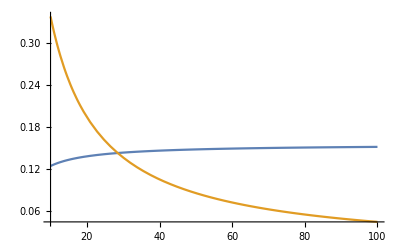

```mathematica
Plot[{T[s],μ[s]},{s,10,100}]
```

### Run modules

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
Do[swaveccspectra[i,Tmuscan],{i,Length[Tmuscan]}]//AbsoluteTiming
```

```mathematica
Do[swaveccuspectra[i,Tmuscan],{i,Length[Tmuscan]}]//AbsoluteTiming
```

```mathematica
Do[swavecclspectra[i,Tmuscan],{i,Length[Tmuscan]}]//AbsoluteTiming
```

## Continuum Energies

```mathematica
2Mc+Table[ReV[100000,mDcalmu[Tmuscan[[i,2]],Tmuscan[[i,3]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tmuscan]}]
```

{3.49286,3.64671,3.67382,3.66679,3.65481,3.64373,3.63444,3.62678,3.62045,3.61516,3.6107,3.60689,3.60361,3.60075,3.59825,3.59603,3.59406,3.5923,3.59071,3.589,3.57989,3.57522,3.57239,3.57048,3.56911,3.56809,3.56728,3.56664,3.56373,3.56276,3.56227,3.56198,3.56178,3.56164,3.56154,3.56146,3.56139}

```mathematica
2Mc+Table[ReV[100000,mDcalmu[Tmuscan[[i,2]],Tmuscan[[i,3]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tmuscan]}]
```

{3.68793,3.99625,4.07568,4.07253,4.05336,4.03386,4.01705,4.00306,3.99145,3.98176,3.97358,3.96661,3.96062,3.95541,3.95085,3.94682,3.94324,3.94004,3.93716,3.93407,3.91765,3.90928,3.90421,3.90081,3.89838,3.89655,3.89513,3.89398,3.88883,3.88711,3.88625,3.88573,3.88538,3.88514,3.88495,3.88481,3.88469}

```mathematica
2Mc+Table[ReV[100000,mDcalmu[Tmuscan[[i,2]],Tmuscan[[i,3]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tmuscan]}]
```

{3.36246,3.46071,3.47344,3.4657,3.45583,3.44715,3.43999,3.43414,3.42931,3.42529,3.4219,3.41901,3.41652,3.41436,3.41246,3.41078,3.40928,3.40795,3.40674,3.40544,3.39852,3.39497,3.39281,3.39136,3.39032,3.38953,3.38892,3.38843,3.38621,3.38547,3.3851,3.38487,3.38472,3.38462,3.38454,3.38447,3.38442}